# QNM Schwarzchild-de Sitter: de Sitter Limit Scenario

Copyright: Yi Zhou; Rodrigo Panosso Macedo (2025)
ArXiv-gr-qc: 2507.05370
PRD       (2025)

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
(*$Assumptions={M>0}*)
```

/Users/qtc325/Trabalhos/HypeBHPT/SdS_QNM

## SdS ExtremalLimit: Functions and Hyperboloidal approach

```mathematica
rΛ= rh/η;
ro=- rh/ο;
Subsο=Solve[{ro+rh+rΛ==0},ο][[1]]
a=-r^2 Λ/3*(1-rh/r)(1-rΛ/r)(1-ro/r)
b=a

λ=rh/(1-η); (*de Sitter scale*)
```

{ο→η/(1+η)}

-1/3 r^2 (1-rh/r) (1-rh/(r η)) Λ (1+rh/(r ο))

-1/3 r^2 (1-rh/r) (1-rh/(r η)) Λ (1+rh/(r ο))

```mathematica
a$par=1-2MM/r - Λ*r^2/3
diff$a=Collect[a-a$par/.Subsο,r]
Coef0=Coefficient[diff$a,r,0]
Coefm1=Coefficient[diff$a,r,-1]
Coefp1=Coefficient[diff$a,r,1]
```

1-(2 MM)/r-(r^2 Λ)/3

-1-(rh^2 Λ)/(3 η)+(rh^2 (1+η) Λ)/(3 η^2)+(rh^2 (1+η) Λ)/(3 η)+(2 MM-(rh^3 (1+η) Λ)/(3 η^2))/r+r ((rh Λ)/3+(rh Λ)/(3 η)-(rh (1+η) Λ)/(3 η))

-1-(rh^2 Λ)/(3 η)+(rh^2 (1+η) Λ)/(3 η^2)+(rh^2 (1+η) Λ)/(3 η)

2 MM-(rh^3 (1+η) Λ)/(3 η^2)

(rh Λ)/3+(rh Λ)/(3 η)-(rh (1+η) Λ)/(3 η)

```mathematica
SubsΛ=Solve[Coef0==0,Λ][[1]]
SubsM=Solve[Coefm1==0,MM][[1]]
SubsΛM=Solve[{Coef0==0,Coefm1==0},{Λ,MM}][[1]]//FullSimplify
SubsΛMExtreme=SubsΛM/.η->1
```

{Λ→(3 η^2)/(rh^2 (1+η+η^2))}

{MM→(rh^3 (1+η) Λ)/(6 η^2)}

{Λ→(3 η^2)/(rh^2 (1+η+η^2)),MM→(rh (1+η))/(2 (1+η+η^2))}

{Λ→1/rh^2,MM→rh/3}

```mathematica
f=a
fExtreme=f/.Subsο/.SubsΛM/.η->1

z=Sqrt[a/b]

rTort$Ext=Integrate[1/fExtreme,r]//FullSimplify
```

-1/3 r^2 (1-rh/r) (1-rh/(r η)) Λ (1+rh/(r ο))

-(r^2 (1-rh/r)^2 (1+(2 rh)/r))/(3 rh^2)

1

1/3 rh ((3 rh)/(r-rh)-2 Log[r-rh]+2 Log[r+2 rh])

```mathematica
func$r[σ_]:= λ/σ (ρρ0 + ρρ1 * σ)
Subsρ=Solve[    {func$r[1]==rh, func$r[σΛ]==rΛ},{ρρ0,ρρ1}     ] [[1]]

ρ1=ρρ1/.Subsρ
ρ0=ρρ0/.Subsρ

ρ[σ_]:=ρ0+ρ1*σ
β=ρ[σ]-σ*D[ρ[σ],σ]//FullSimplify
```

{ρρ0→-((-1+η)^2 σΛ)/(η (-1+σΛ)),ρρ1→((-1+η) (η-σΛ))/(η (-1+σΛ))}

((-1+η) (η-σΛ))/(η (-1+σΛ))

-((-1+η)^2 σΛ)/(η (-1+σΛ))

-((-1+η)^2 σΛ)/(η (-1+σΛ))

```mathematica
r$of$σ[σ_]:=λ ρ[σ]/σ//FullSimplify
r$of$σ[σ]

dr$dσ=D[r$of$σ[σ],σ];

σ$of$r=σ/.Solve[r$of$σ[σ]==r,σ][[1]]

σh=σhrz/.Solve[r$of$σ[σhrz]==rh,σhrz][[1]]

σΛ=σcauchy/.Solve[r$of$σ[σcauchy]==rΛ,σcauchy][[1]]
σο=σo/.Solve[r$of$σ[σo]==ro,σo][[1]]/.Subsο//FullSimplify
```

(-rh η σ+rh (-1+η+σ) σΛ)/(η σ (-1+σΛ))

(rh (-1+η) σΛ)/(-r η+rh η-rh σΛ+r η σΛ)

1

σΛ

(σΛ-η σΛ)/(-1+η (-2+σΛ)+2 σΛ)

```mathematica
F=Collect[Simplify[f/.r->r$of$σ[σ]]/.Subsο/.SubsΛM,σ]//FullSimplify
ζ=Simplify[z/.r->r$of$σ[σ]]
Ξ=ζ*β//FullSimplify

dx$dσ=FullSimplify[-β/(σ^2F)]
```

((-1+η)^2 (-1+σ) (σ-σΛ) σΛ ((-1+η) σΛ+σ (-1+η (-2+σΛ)+2 σΛ)))/((1+η+η^2) σ^2 (-1+σΛ)^2 (η σ+σΛ-(η+σ) σΛ))

1

-((-1+η)^2 σΛ)/(η (-1+σΛ))

((1+η+η^2) (-1+σΛ) (η σ+σΛ-(η+σ) σΛ))/(η (-1+σ) (σ-σΛ) ((-1+η) σΛ+σ (-1+η (-2+σΛ)+2 σΛ)))

```mathematica
x$BHHrz = (rh Log[1-σ])/((-2+(3 (1+η))/(1+η+η^2)) λ)
x$CosmoHrz = (rh Log[σ-σΛ])/(η (1-3/(1+η+η^2)) λ)
x$NegativeHrz = (rh (1+η) (1+η+η^2) Log[σ+((-1+η) σΛ)/(-1+η (-2+σΛ)+2 σΛ)])/(η (2+5 η+2 η^2) λ)
```

((1-η) Log[1-σ])/(-2+(3 (1+η))/(1+η+η^2))

((1-η) Log[σ-σΛ])/(η (1-3/(1+η+η^2)))

((1-η) (1+η) (1+η+η^2) Log[σ+((-1+η) σΛ)/(-1+η (-2+σΛ)+2 σΛ)])/(η (2+5 η+2 η^2))

```mathematica
x$Reg = CONSTANT
x=x$BHHrz+x$CosmoHrz+x$NegativeHrz+x$Reg//FullSimplify
```

CONSTANT

CONSTANT+((1+η+η^2) Log[1-σ])/(1+2 η)-((1+η+η^2) Log[σ-σΛ])/(η (2+η))-((-1+η) (1+η) (1+η+η^2) Log[σ+((-1+η) σΛ)/(-1+η (-2+σΛ)+2 σΛ)])/(η (2+5 η+2 η^2))

```mathematica
H= x$BHHrz-x$CosmoHrz-x$NegativeHrz
dH$dσ=FullSimplify[D[H,σ]];
```

((1-η) Log[1-σ])/(-2+(3 (1+η))/(1+η+η^2))-((1-η) Log[σ-σΛ])/(η (1-3/(1+η+η^2)))-((1-η) (1+η) (1+η+η^2) Log[σ+((-1+η) σΛ)/(-1+η (-2+σΛ)+2 σΛ)])/(η (2+5 η+2 η^2))

```mathematica
p=-1/dx$dσ
γ=dH$dσ*p//FullSimplify
w=(1-γ^2)/p//FullSimplify
```

-(η (-1+σ) (σ-σΛ) ((-1+η) σΛ+σ (-1+η (-2+σΛ)+2 σΛ)))/((1+η+η^2) (-1+σΛ) (η σ+σΛ-(η+σ) σΛ))

(2 η^2 (1+σ (-2+σΛ)) (σ-σΛ)+(-1+σ) (-1+σΛ) σΛ+η (-1+2 σ-σΛ) (-σΛ+σ (-1+2 σΛ)))/((1+2 η) (-1+σΛ) (-η σ+(-1+η+σ) σΛ))

(4 (1+η+η^2) (-η^2 (σ-σΛ) (-2+σΛ)+σΛ-σΛ^2+η (σ+σΛ-2 σ σΛ)))/((1+2 η)^2 (-1+σΛ) (-η σ+(-1+η+σ) σΛ))

```mathematica
V=f*( l*(l+1)/r^2 + D[f,r]/r)/.SubsΛM/.r->r$of$σ[σ]//FullSimplify;

q=λ^2/p * V/.Subsο//Expand//FullSimplify
```

1/((1+η+η^2) σ^2 (-1+σΛ) (η σ+σΛ-(η+σ) σΛ)^3)η σΛ (-η^3 (σ-σΛ) (σ^2 (-2+l (1+l) (-1+σΛ)^2)+4 σ σΛ-2 σΛ^2)+(-1+σ) σΛ (l σ^2 (-1+σΛ)^2+l^2 σ^2 (-1+σΛ)^2-2 (-1+σ)^2 σΛ^2)+η^2 (6 σΛ^3-6 σ σΛ^2 (2+σΛ)+6 σ^2 σΛ (1+2 σΛ)+σ^3 (-1+l (-1+σΛ)^3+l^2 (-1+σΛ)^3+σΛ (-3+(-3+σΛ) σΛ)))+η (-6 σΛ^3-6 σ^2 σΛ^2 (2+σΛ)+6 σ σΛ^2 (1+2 σΛ)+σ^3 (-1+l (-1+σΛ)^3+l^2 (-1+σΛ)^3+σΛ (3+σΛ (3+σΛ)))))

```mathematica
η = 1 - ϵ;
```

```mathematica
P$ext=p/.ϵ->0//FullSimplify
%/.σΛ->1/2//FullSimplify
```

((-1+σ) (σ-σΛ))/(-1+σΛ)

-1+(3-2 σ) σ

```mathematica
γ$ext=γ/.ϵ->0//FullSimplify
%/.σΛ->1/2//FullSimplify
```

-1+(2 (-1+σ))/(-1+σΛ)

3-4 σ

```mathematica
W$ext=w/.ϵ->0//FullSimplify
%/.σΛ->1/2//FullSimplify
```

-4/(-1+σΛ)

8

```mathematica
Q$ext=q/.ϵ->0//FullSimplify
%/.σΛ->1/2//FullSimplify
```

-(l (1+l) σΛ)/(σ^2 (-1+σΛ))

(l (1+l))/σ^2

## QNM Eigenvalue Solver

## Physical Parameters

```mathematica
spin=0; (*SCALAR PERTURBATIONS*) (*NOTE: SO FAR, ONLY POTENTIAL FOR SCALAR FIELD IS IMPLEMENTED*)
l=2; (*ANGULAR MODE*)
σΛ=1/2; (*Coordinate Location of Cosmological Horizon*)
```

## Discrete Functions and Matrices

### Spectral Routines

#### Chebyshev Coefficients

```mathematica
ChebGaussCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[ Cos[Pi*(j+1/2)/(Nf+1)] ,Prec];

c=Table[  2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,0,Nf}]  /nf        ,{m,0,Nf}]
];

ChebLobattoCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[Cos[j π/Nf],Prec];

c=Table[  ( 2-KroneckerDelta[m,Nf]) /(2Nf) (  f[[1]]+(-1)^m f[[nf]] + 2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,1,Nf-1}]  )        ,{m,0,Nf}]
];
```

#### Spectral Differentiation matrices

```mathematica
DiffMatrix[a_,b_,Nz_,Prec_]:=Module[
{k,i,j,dx, Δ,Dy},

k[i_]:=If[i*(i-Nz)==0, 2,1];
dx[i_,j_]:=If[i!=j,
k[i]*(-1)^(i-j)/(k[j]*(x[i,Nz]-x[j,Nz])),
0
];
Δ=b-a;
Dy=N[2/Δ * Table[dx[i,j], {i,0,Nz}, {j,0,Nz}],Prec ];

For[i=0, i<=Nz, i++,
Dy[[i+1,i+1]]= -Sum[ Dy[[i+1,j+1]], {j,0,Nz} ];
];
Dy
]
```

#### Chebyshev Interpolation

```mathematica
ChebInterpolation[c_,a_,b_,x_]:=Module[
{nc, Nc},
nc=Length@c;
Nc=nc-1;

y=(2 x-(a+b))/(b-a);

c[[1]]/2+Sum[c[[i+1]]*ChebyshevT[i,y],{i,1,Nc}]
];

ChebyLobattoInterpolationVector[xl_,Nl_,xα_,Prec]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα]/(Nl),{j,1,Nl}]
]
],
{l,0,Nl}
]

];

ChebyLobattoInterpolationMatrix[xl_,Nl_,xα_,Nα_,Prec]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα[[α+1]]]/(Nl),{j,1,Nl}]
]
],
{α,0,Nα},{l,0,Nl}
]

]
```

#### Chebyshev Integration

```mathematica
DefiniteIntegral[c_,a_,b_]:=Module[
{kf,nc,Nc, Int},
nc=Length@c;
Nc=nc-1;
kf=Floor[Nc/2];
Int=c[[1]]- 2Sum[c[[2 k +1]]/(4 k ^2 -1),{k,1,kf}];
(b-a)*Int/2
];

ChebyLobattoHilbertIntegration[z_,Nz_,Prec_]:=Module[
{i,j},
Table[
If[i!=j,
0,
If[i==0 || i==Nz,
(1/Nz - Sum[(2-KroneckerDelta[2k,Nz])/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}]),
(2/Nz - 2Sum[(2-KroneckerDelta[2k,Nz])*ChebyshevT[2k,z[[i+1]]]/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}])
]
],
 {i,0,Nz}, {j,0,Nz}
]
]
```

### Numerical parameters

```mathematica
Prec=10*MachinePrecision;
x=.
z0=σΛ
z1=σh

Δz=z1-z0;

Nz=100;
nz=Nz+1; (*Total number of points*)

x[i_,Nz_]:=Cos[(π i)/Nz];
(*x[i_,Nz_]:=Cos[(π (i+1/2))/(Nz+1)];*)

χ=N[Table[x[i,Nz],{i,0,Nz}],Prec];
ZeroArray=ConstantArray[0,nz];
(*z=N[Table[z0+1/2 Δz (1+x[i,Nz]),{i,0,Nz}],Prec];

ListPlot[Transpose@{z,ZeroArray}, AxesLabel->{"σ",""}]*)
```

1/2

1

#### AnMR Parameter

0

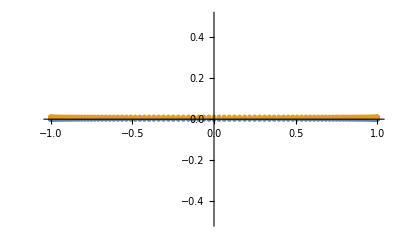

```mathematica
xb=1;
κ=0
If[κ==0,
(*CONDITION WHEN κ==0*)
X=χ;
z=N[z0+1/2 Δz*(1+X),Prec]
,
(*CONDITION WHEN κ!=0*)
X=N[xb*(1-2*Sinh[κ*(1-xb*χ)]/Sinh[2*κ]),Prec];
z=N[z0+1/2 Δz*(1+X),Prec]
];

ListPlot[{Transpose@{χ,ZeroArray},Transpose@{X,ZeroArray+0.01}}, PlotRange->{-0.5,0.5}]
```

### Discrete Functions

```mathematica
pVec=P$ext/.σ->z;
dpVec=D[P$ext,σ]/.σ->z;
PotVec=Q$ext/.σ->z;(*Limit[Pot,σ->z]*)
γVec=γ$ext/.σ->z;
dγVec=D[γ$ext,σ]/.σ->z;

wVec=W$ext/.σ->z;
```

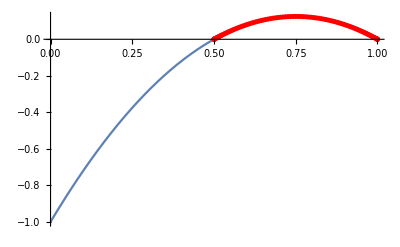

```mathematica
Plot$p=Plot[P$ext,{σ,0,σh}];
Plot$pVec=ListPlot[Transpose@{z,pVec}, PlotStyle->Red];
Show[Plot$p,Plot$pVec]
```

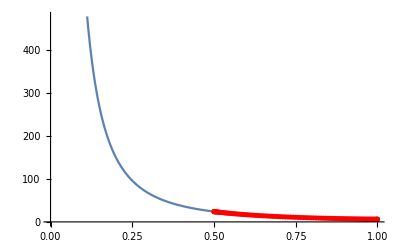

```mathematica
Plot$Pot=Plot[Q$ext,{σ,0,σh}];
Plot$PotVec=ListPlot[Transpose@{z,PotVec}, PlotStyle->Red];
Show[Plot$Pot,Plot$PotVec]
```

### Differentiation Matrices

[Calculating the discrete representation of the derivate operator δσ ---> Dσ]

#### Create directory to store differentiation matrices

```mathematica
DirName$Matrices="OperatorMatrix";
If[!DirectoryQ[DirName$Matrices],CreateDirectory[DirName$Matrices]]
```

#### Create or Load Matrices

```mathematica
fn$Dχ="OperatorMatrix/Dchi_"<>"N_"<>ToString[Nz]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_"<>"N_"<>ToString[Nz]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dχ=FileExistsQ[fn$Dχ];
check$D2χ=FileExistsQ[fn$D2χ];

If[!check$Dχ || !check$D2χ, 
Print["Calculating Differentiation Matrices"];

Dχ=DiffMatrix[-1,1,Nz,Prec]; 
D2χ=Dχ . Dχ;

Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ],"Table"];,

Print["Loading Differentiation Matrices"];
Dχ=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id=IdentityMatrix[Nz+1];
Zero=ConstantArray[0,{Nz+1,Nz+1}];
```

Loading Differentiation Matrices

#### Analytical Mesh Refiniment

```mathematica
If[κ==0,
(*CONDITION κ ==0*)
Dx=Dχ;
D2x=D2χ
,
(*CONDITION κ != 0*)
J=N[ 2*κ*Cosh[κ*(1-χ*xb)]/Sinh[2*κ],Prec];
J2=N[ -2*κ^2*xb*Sinh[κ*(1-χ*xb)]/Sinh[2*κ],Prec];

Dx = N[Dχ/J,Prec];
D2x = N[(D2χ - J2*Dx)/J^2,Prec]
];
```

#### Map into σ ∈ [0,σh]

```mathematica
Dσ=2/Δz Dx;
D2σ=(2/Δz)^2 D2x;
```

## QNM Eigenvalue Problem

### Discrete ODE operators

```mathematica
LL1=pVec*D2σ + dpVec*Dσ - PotVec*Id;

L2=2*γVec*Dσ + dγVec*Id;

L=N[ArrayFlatten[{
{Zero,Id} , 
{LL1/wVec,L2/wVec} 
}
],
Prec];
```

### Solve Eigenvalue

```mathematica
Print["Calculating QNM"];
EigenSol=Eigenvalues[L];
Print["Done"];
```

Calculating QNM

Done

#### Re-scale Laplace to Fourier

```mathematica
ω=-I*EigenSol;
```

#### Filter discrete from continuous spectra

```mathematica
PosQNM=Position[EigenSol,x_/;Im@x!=0]//Flatten;

nQNM=Length@PosQNM;
ω$QNM=Table[ω[[PosQNM[[i]]]],{i,1,nQNM}];

PosBranch=Position[EigenSol,x_/;Im@x==0]//Flatten;
nBranch=Length@PosBranch;
ω$BranchCut=Table[ω[[PosBranch[[i]]]],{i,1,nBranch}];

QNMData=Table[{Re@ω$QNM[[iqnm]],Im@ω$QNM[[iqnm]]},{iqnm,1,Length@ω$QNM}];
BranchCutData=Table[{Re@ω$BranchCut[[iqnm]],Im@ω$BranchCut[[iqnm]]},{iqnm,1,Length@ω$BranchCut}];
```

#### Plot

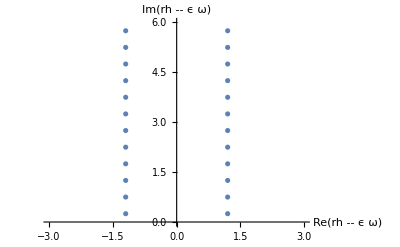

```mathematica
ListPlot[{QNMData,BranchCutData},
AxesLabel->{"Re("<>ToString[λ]<>" ω)","Im("<>ToString[λ]<>" ω)"}, PlotRange->{{-3,3},{0,6}}]
```

#### Individual Overtones

```mathematica
Print["Fundamental mode n = 0"]
N[ω$QNM[[-1]],20]
N[ω$QNM[[-2]],20]
Print["First Overtone n = 1"]
N[ω$QNM[[-3]],20]
N[ω$QNM[[-4]],20]
Print["Second Overtone = 2"]
N[ω$QNM[[-5]],20]
N[ω$QNM[[-6]],20]
```

Fundamental mode n = 0

-1.1989578808281798854+0.25 ⅈ

1.1989578808281798854+0.25 ⅈ

First Overtone n = 1

-1.1989578808281798854+0.75 ⅈ

1.1989578808281798854+0.75 ⅈ

Second Overtone = 2

-1.198957880828179885+1.25 ⅈ

1.198957880828179885+1.25 ⅈ

### Export Data

```mathematica
DirName$Data="Data/ExtremalLimit";
If[!DirectoryQ[DirName$Data],CreateDirectory[DirName$Data]]
```

/Users/qtc325/Trabalhos/HypeBHPT/SdS_QNM/Data/ExtremalLimit

```mathematica
Print["Export Data"];
fn=DirName$Data<>"/QNM_N_"<>ToString[Nz]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

Export[fn,N[QNMData,Prec],"Table"]
fn=DirName$Data<>"/Branch_N_"<>ToString[Nz]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
Export[fn,N[BranchCutData,Prec],"Table"]

Print["Done"]
```

Export Data

Data/ExtremalLimit/QNM_N_100_l2_spin0_Prec_159.dat

Data/ExtremalLimit/Branch_N_100_l2_spin0_Prec_159.dat

Done